## Function definitions

```mathematica
(* Integral kernels D (r,r',ξ) and D (x,x',ξ): *)
Kern1D[x_,xp_,ξ_]=Sqrt[ⅈ/(2*Pi*Sin[ξ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ]-(2*xp*x)/Sin[ξ])];
Kern[x_,xp_,y_,yp_,ξ_]=ⅈ/(2*Pi*Sin[ξ])*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ]-(2*xp*x)/Sin[ξ]+(yp^2+y^2)/Tan[ξ]-(2*y*yp)/Sin[ξ])];
```

Pump spot :

```mathematica
(* Pump profiles (1D, 2D, integral) *)

Clear[fp,σ]
pump1D[x_,fp_,σ_]=Sqrt[fp]*Exp[-x^2/(2σ^2)];
pump[x_,y_]=fp*Exp[-(x^2+y^2)/(2σ^2)];
(*pumpterm[x_,y_,ξ_]=Integrate[Integrate[pump[xp,yp]*Kern[x,xp,y,yp,ξ],{xp,-200,200}],{yp,-200,200}];*)
```

## LHO

```mathematica
lambda0=780*10^-9;
zA=0;
zR=5*10^-3; 
eta=1;
w0=N[Sqrt[lambda0*zR/Pi]]
lho=(eta*w0)/Sqrt[2]
```

0.0000352336

0.0000249139

```mathematica
mA=1.42*10^(-25);
hbar=1.0545718*10^(-34);
omegaT=1000;
lho2=Sqrt[hbar/(mA*omegaT)]
```

8.61775×10^-7

```mathematica
w02=(eta*lho2)/Sqrt[2]
```

6.09367×10^-7

## Mehler kernel checks

```mathematica
FullSimplify[Sinh[ⅈ x]]
```

Cos[x]

```mathematica
ρ=Exp[-ⅈ ξ]
```

ⅇ^(-ⅈ ξ)

```mathematica
FullSimplify[ρ/(1-ρ^2)]
```

-1/2 ⅈ Csc[ξ]

```mathematica
FullSimplify[1/2+ρ^2/(1-ρ^2)]
```

-1/2 ⅈ Cot[ξ]

```mathematica
exppart[a_]=FullSimplify[Exp[-(x^2+xp^2)/2]*Exp[-Exp[-2 a]/(1-Exp[-2 a])(x^2+xp^2)]*Exp[(2 Exp[-a])/(1-Exp[-2 a])(x xp)]];
```

```mathematica
amplpart[a_]=FullSimplify[Sqrt[2/Pi] Exp[-a/2]/Sqrt[1-Exp[-2 a]],Assumptions->a∈Reals]
```

1/(√π √Sinh[a])

```mathematica
amplpart[ a]*exppart[a]
amplpart[ⅈ a]*exppart[ⅈ a]
```

(ⅇ^(-1/2 (-2 x xp+(x^2+xp^2) Cosh[a]) Csch[a]))/(√π √Sinh[a])

(ⅇ^(1/2 ⅈ (-2 x xp+(x^2+xp^2) Cos[a]) Csc[a]))/(√π √(ⅈ Sin[a]))

```mathematica
FullSimplify[(Exp[-ⅈ a]+Exp[ⅈ a])/(Exp[ⅈ a]-Exp[-ⅈ a])]
```

-ⅈ Cot[a]

```mathematica
FullSimplify[(1+Exp[-2a])/(1-Exp[-2a])]
```

True

## Plotting kernels

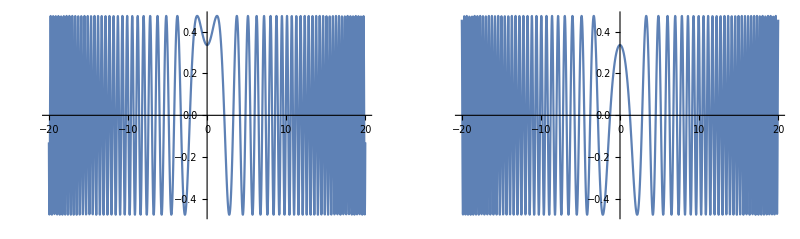

```mathematica
GraphicsGrid[{{Plot[Re[Kern1D[0,xp,Pi/4]],{xp,-20,20}],Plot[Im[Kern1D[0,xp,Pi/4]],{xp,-20,20}]}}]
```

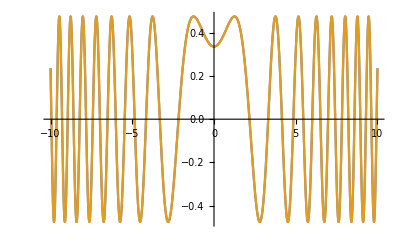

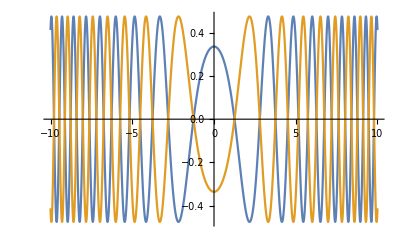

```mathematica
Plot[{Re[Kern1D[x,0,Pi/4]],Re[Kern1D[x,0,-Pi/4]]},{x,-10,10}]
Plot[{Im[Kern1D[x,0,Pi/4]],Im[Kern1D[x,0,-Pi/4]]},{x,-10,10}]
```

## Analytic integral for smoothing fn

```mathematica
(* Doing the integral with arbitrary coefficients obeying the conditional expr *)
```

```mathematica
res=Integrate[AA Exp[-a x^2+b x-c xp^2+d xp+e x xp+f],{xp,-∞,∞},Assumptions->Re[a]>0&&Re[c]>0&&Re[-4 c+e^2/a]<0]
```

(AA ⅇ^((d^2+2 d e x+e^2 x^2+4 c (f+x (b-a x)))/(4 c)) √π)/(√c)

```mathematica
(* Replacing coefficients with proper factors *)
```

```mathematica
replacements[ξ_,l_]={AA->1/(2 Pi l^2) Sqrt[ⅈ/(Pi Sin[ξ])],a->-(1/(2 l^2)+ⅈ/(2 Tan[ξ])),b->y/l^2,c->-(1/(2 l^2)+ⅈ/(2 Tan[ξ])),d->yp/l^2,e->ⅈ/Sin[ξ],f->-(y^2+yp^2)/(2 l^2)}
```

{AA→(√(ⅈ Csc[ξ]))/(2 l^2 π^(3/2)),a→-1/(2 l^2)-1/2 ⅈ Cot[ξ],b→y/l^2,c→-1/(2 l^2)-1/2 ⅈ Cot[ξ],d→yp/l^2,e→ⅈ Csc[ξ],f→(-y^2-yp^2)/(2 l^2)}

```mathematica
SimplifiedResult[y_,yp_,ξ_,l_]=FullSimplify[res/.replacements[ξ,l],Assumptions->l>0&&ξ∈Reals]
```

(ⅇ^(-(ⅈ ((1+l^4) x^2+2 x y-y^2-2 yp^2)+l^2 ((-2 x^2-2 x y+y^2+yp^2) Cot[ξ]+2 x yp Csc[ξ]))/(2 l^2 (-ⅈ+l^2 Cot[ξ]))) √(ⅈ Csc[ξ]))/(l^2 π √(-2/l^2-2 ⅈ Cot[ξ]))

```mathematica
(* check that assumptions work *)
```

```mathematica
FullSimplify[ComplexExpand[Re[4c-e^2/a]<0/.replacements[ξ,l]],Assumptions->l>0&&ξ∈Reals]
FullSimplify[ComplexExpand[Re[a]<0/.replacements[ξ,l]],Assumptions->l>0]
```

True

True

## Smoothing fn stuff

```mathematica
fp=10;
σ=20;
```

```mathematica
SmoothingFn[x_,y_,xp_,yp_,L_,power_]=1/(2 Pi L^2)*Exp[-(x-y)^power/(2L^2)-(xp-yp)^power/(2L^2)];
```

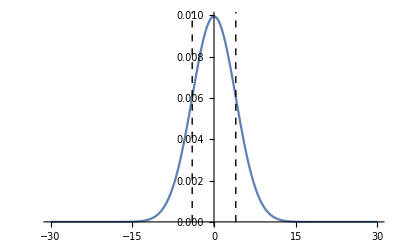

```mathematica
Show[Plot[SmoothingFn[x,0,0,0,4,2],{x,-30,30},PlotRange->Full],Graphics[{{Dashed,Line[{{-4,0},{-4,10}}]},{Dashed,Line[{{4,0},{4,10}}]}}]]
```

```mathematica
(* Coefficients gotten by pen and paper *)
```

```mathematica
Clear[L]
α[ξ_,L_]=ⅈ/(2 Tan[ξ])+1/(2L^2);
β[ξ_,L_]=α[ξ,L]+1/(4*α[ξ,L]*Sin[ξ]^2);
A[ξ_,L_]=1/(2Pi L^2)*Sqrt[(ⅈ*Pi)/(β[ξ,L]*α[ξ,L]*Sin[ξ])];
B[ξ_,L_]=1/(2L^2)-1/(4L^4*β[ξ,L]);
Cc[ξ_,L_]=ⅈ/(4*L^4*α[ξ,L]*β[ξ,L]*Sin[ξ]);
S[x_,xp_,ξ_,L_]=A[ξ,L]*Exp[-B[ξ,L]*(x^2+xp^2)-Cc[ξ,L]*x*xp];
```

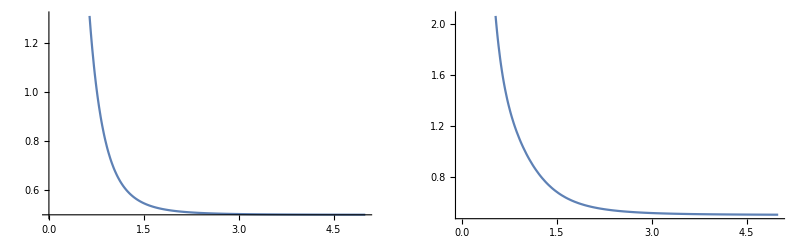

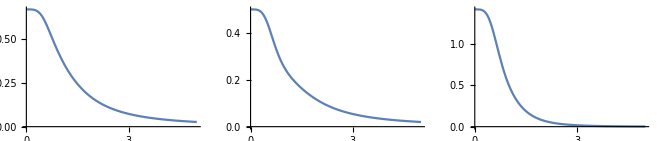

```mathematica
GraphicsGrid[{{Plot[Abs[α[Pi/4,L]],{L,0,5}],Plot[Abs[β[Pi/4,L]],{L,0,5}]}}]
GraphicsGrid[{{Plot[Abs[A[Pi/4,L]],{L,0,5},ImageSize->200],Plot[Abs[B[Pi/4,L]],{L,0,5},ImageSize->200],Plot[Abs[Cc[Pi/4,L]],{L,0,5},ImageSize->200]}}]
```

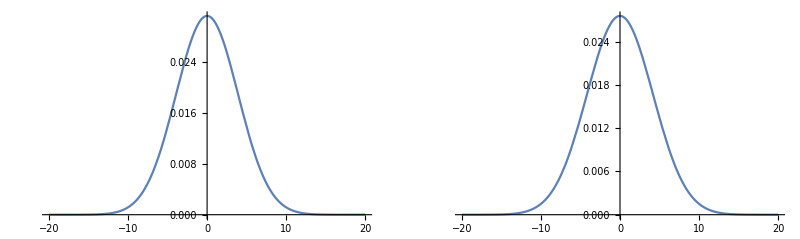

```mathematica
GraphicsGrid[{{Plot[Re[S[0,xp,Pi/4,4]],{xp,-20,20},PlotRange->All],Plot[Im[S[0,xp,Pi/4,4]],{xp,-20,20},PlotRange->Full]}}]
```

```mathematica
(* Sampling the smoothed fn discretely *)
Clear[L]
pumpsmoothdisc[x_,L_]=Sum[pump[x,xp]*S[x,xp,Pi/4,L],{xp,-32,32,L}];
```

```mathematica
(* Making the sampling lattice spacing small - TAKES A WHILE *)
```

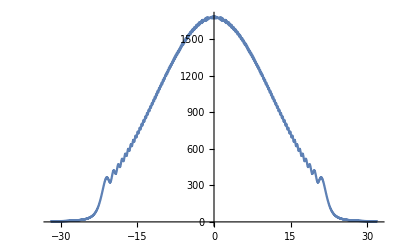

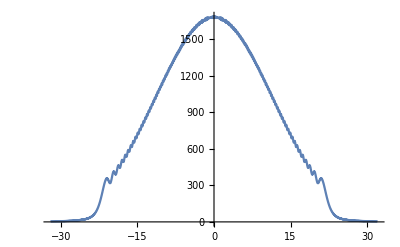

```mathematica
L=0.01;
pumpdisc[x_]=Sum[pump[xp,x]*Kern1D[x,xp,Pi/4],{xp,-32,32,L}];
disc=Table[{x,Abs[pumpdisc[x]]},{x,-32,32,L}];
discsmooth=Table[{x,Abs[pumpsmoothdisc[x,L]]},{x,-32,32,L}];
ListPlot[disc,Joined->True]
ListPlot[discsmooth,Joined->True,PlotRange->All]
```

```mathematica
(* Larger lattice spacing *)
```

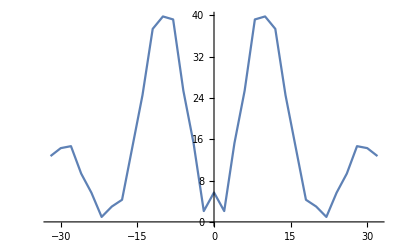

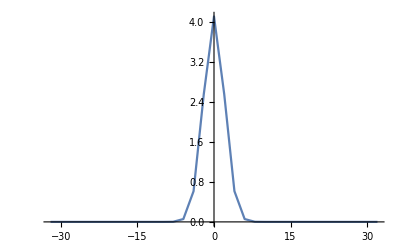

```mathematica
L=2;
pumpdisc[x_]=Sum[pump[xp,x]*Kern1D[x,xp,Pi/4],{xp,-32,32,L}];
disc=Table[{x,Abs[pumpdisc[x]]},{x,-32,32,L}];
discsmooth=Table[{x,Abs[pumpsmoothdisc[x,L]]},{x,-32,32,L}];
ListPlot[disc,Joined->True]
ListPlot[discsmooth,Joined->True,PlotRange->All]
```

```mathematica
(* Comparing the analytic (continuous) results *)
```

```mathematica
int[x_]=Integrate[pump[0,xp]*Kern1D[x,xp,Pi/4],{xp,-100,100}];
intsmooth[x_]=Integrate[pump[0,xp]*S[x,xp,Pi/4,4],{xp,-100,100}];
intsmoothan[x_]=Integrate[pump[0,xp]*Evaluate[SimplifiedResult[x,xp,Pi/4,4]],{xp,-100,100}];
```

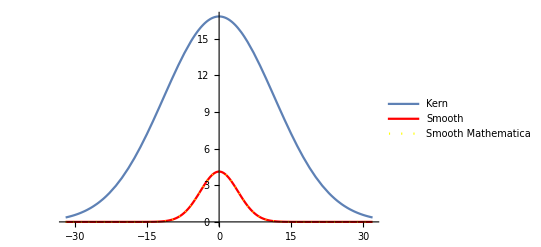

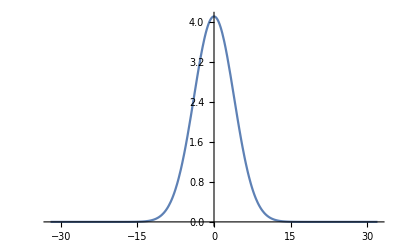

```mathematica
Plot[{Abs[int[x]],Abs[intsmooth[x]],Abs[intsmoothan[x]]},{x,-32,32},PlotLegends->{"Kern","Smooth","Smooth Mathematica"},PlotStyle->{Normal,{Thick,Red},{Dotted,Yellow}}]
Plot[Abs[intsmooth[x]],{x,-32,32}]
```

```mathematica
(* Comparing results after convolving only one side of D*f with S *)
```

```mathematica
smoothpump[y_,yp_,L_]=Integrate[pump[x,xp]*SmoothingFn[x,y,xp,yp,L,2],{x,-100,100},{xp,-100,100}];
```

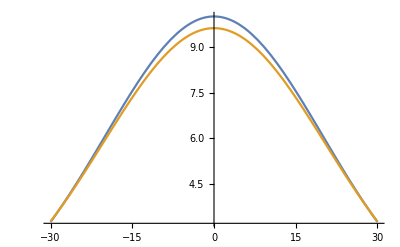

```mathematica
Plot[{pump[x,0],smoothpump[x,0,4]},{x,-30,30}]
```

## Checking interaction term for α(r) eqn instead

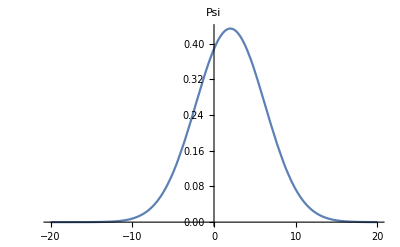

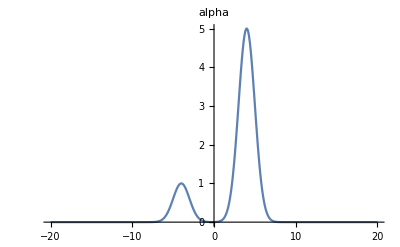

```mathematica
(* The int term contains a double convolution with the atom field intensity, which is smooth -- assume Gaussian. We also take alpha to be some smooth function to compare things *)
shiftpsi=2;
shiftalpha=-4;
peakalpha=5;
(*σP=20;*)
Psi[x_,σ_]=1/Sqrt[Sqrt[Pi] σ](Exp[-(x-shiftpsi)^2/(4 σ^2)]);
alpha[xp_]=Exp[-(xp-shiftalpha)^2/2]+peakalpha*Exp[-(xp+shiftalpha)^2/2];

Plot[Psi[x,3],{x,-20,20},PlotLabel->"Psi", PlotRange->All]
Plot[alpha[x],{x,-20,20},PlotLabel->"alpha",PlotRange->All]
```

```mathematica
(* Convolution X=D(θ)*|psi|^2*D(-θ) *)
```

```mathematica
X[x_,xp_,θ_,σ_]=Integrate[Kern1D[x,xpp,θ]*Abs[Psi[xpp,σ]]^2*Kern1D[xpp,xp,-θ],{xpp,-∞,∞},Assumptions->σ ∈Reals&&σ>0]
```

(√2 ⅇ^(-1/2 (x-xp) (ⅈ (x+xp) Cot[θ]+Csc[θ] (-4 ⅈ+(x-xp) σ^2 Csc[θ]))) √(Csc[θ]^2))/π

```mathematica
(* Plotting X *)
```

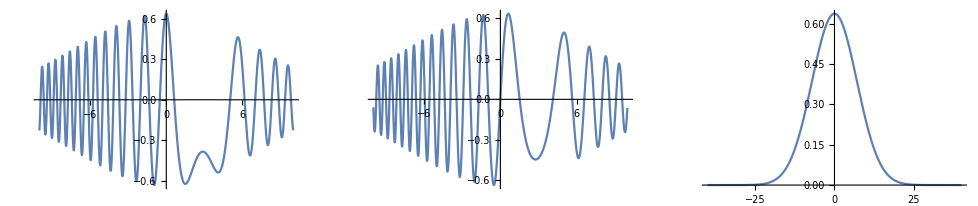

```mathematica
σP=0.1;
GraphicsGrid[{{Plot[Re[X[x,0,Pi/4,σP]],{x,-10,10},PlotRange->All,ImageSize->300],Plot[Im[X[x,0,Pi/4,σP]],{x,-10,10},PlotRange->All,ImageSize->300],
Plot[Abs[X[x,0,Pi/4,σP]],{x,-40,40},PlotRange->All,ImageSize->300]}}]
```

```mathematica
(* Sampling discretely X *)
```

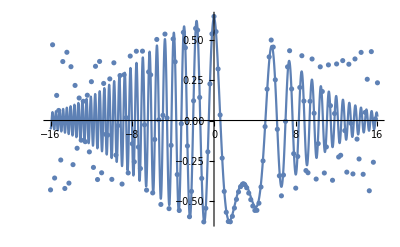

```mathematica
L=0.2;
mult=1/30;
ls=16;
Xdisc[x_,xp_,θ_]=Sum[L*Kern1D[x,xpp,θ]*Abs[Psi[xpp,σP]]^2*Kern1D[xpp,xp,-θ],{xpp,-ls,ls,L}];
Xdisctable=Table[{x,Re[Xdisc[x,0, π/4]]},{x,-ls,ls,L}];
Show[{ListPlot[Xdisctable],Plot[Re[X[x,0,Pi/4,σP]],{x,-ls,ls}]}]
```

```mathematica
(* Continuous version of what the integral of X.α would be *)
```

```mathematica
Xα[x_]=Integrate[X[x,xp,Pi/4,σP]*alpha[xp],{xp,-∞,∞}];
```

```mathematica
Xαdisc[x_]=Sum[L*Xdisc[x,xp,Pi/4]*alpha[xp],{xp,-ls,ls,L}];
Xαdisctable=Table[{x,Re[Xαdisc[x]]},{x,-ls,ls,L}];
αdisctable=Table[{x,Abs[alpha[x]]},{x,-ls,ls,L}];
```

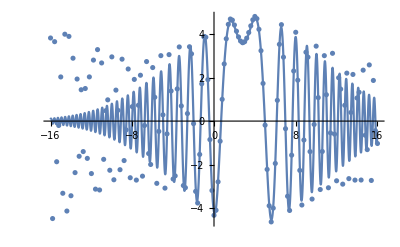

```mathematica
Show[{ListPlot[Xαdisctable],Plot[Re[Xα[x]],{x,-ls,ls}]}]
```

0.0394045

25.3778

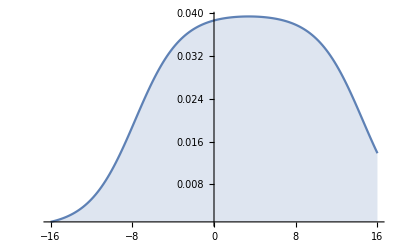

```mathematica
(* Want the value at (one) peak so I can put a line on it (because I liked it but only so so) *)
maxcont=Abs[N[Xαcont[-shiftalpha]]];
maxdisc=Abs[N[Xαdisc[-shiftalpha]]];
maxcont/maxdisc
thisshouldbe1=maxdisc/maxcont
(* Plotting the value of the continuous distribution/discrete distribution at lattice points *)
DiscretePlot[(Abs[N[Xαdisc[q]]]/Abs[N[Xαcont[q]]])^-1,{q,-ls,ls,L},PlotRange->Full]
```

```mathematica
(* Rescaled alpha and X*a *)
```

## α(r) with higher mode suppression

```mathematica
SetDirectory["~/Dropbox/notes-multimode/figures/realspace/debugging"]
```

/home/mls/Dropbox/notes-multimode/figures/realspace/debugging

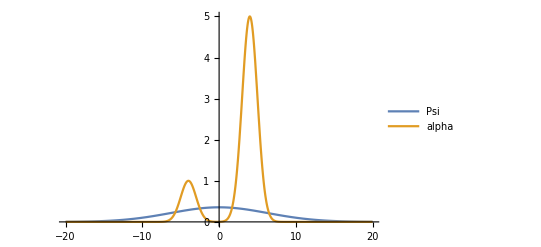

wavefns.png

-Graphics-

```mathematica
(* The int term contains a double convolution with the atom field intensity, which is smooth -- assume Gaussian. We also take alpha to be some smooth function to compare things *)
shiftpsi=0;
shiftalpha=-4;
peakalpha=5;
(*σP=20;*)
Clear[σ]
Psi[x_,σ_]=1/Sqrt[Sqrt[Pi] σ](Exp[-(x-shiftpsi)^2/(4 σ^2)]);
alpha[xp_]=Exp[-(xp-shiftalpha)^2/2]+peakalpha*Exp[-(xp+shiftalpha)^2/2];

plot2=Plot[{Psi[x,Sqrt[20]],alpha[x]},{x,-20,20},PlotLegends->{"Psi","alpha"}, PlotRange->All]
Export["wavefns.png",plot2]
Plot[alpha[x],{x,-20,20},PlotLabel->"alpha",PlotRange->All]
```

```mathematica
KernCutoff[x_,xp_,ξ_,γ_]=Sqrt[ⅈ/(Pi*Sin[ξ+ⅈ γ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
```

```mathematica
(* Convolution X=D(θ)*|psi|^2*D(-θ) *)
```

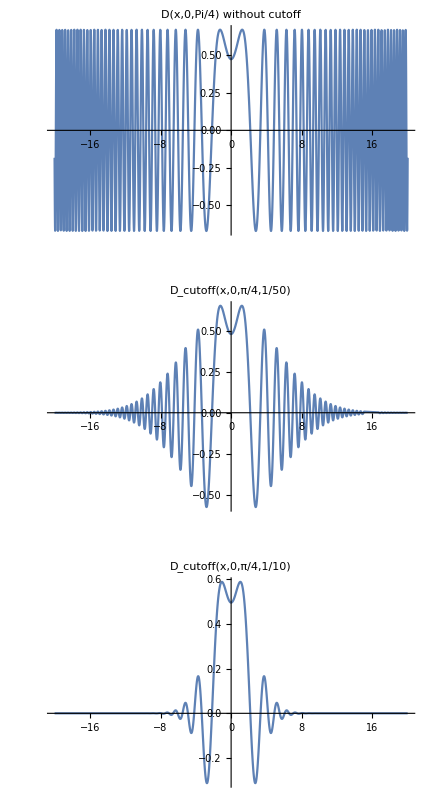

kernelcutoffs.eps

```mathematica
plots1=GraphicsGrid[{{Plot[Re[KernCutoff[x,0,Pi/4,0]],{x,-20,20},ImageSize->400,PlotLabel->"D(x,0,Pi/4) without cutoff"]},{Plot[Re[KernCutoff[x,0,Pi/4,1/50]],{x,-20,20},ImageSize->400,PlotLabel->"D_cutoff(x,0,π/4,1/50)"]},{Plot[Re[KernCutoff[x,0,Pi/4,1/10]],{x,-20,20},ImageSize->400,PlotRange->All,PlotLabel->"D_cutoff(x,0,π/4,1/10)"]}}]
Export["kernelcutoffs.eps",plots1]
```

```mathematica
shiftangle=Pi/2;
```

```mathematica
Manipulate[GraphicsGrid[{{Plot[Re[KernCutoff[x,0,angle,0.0001]],{x,-20,20},PlotRange->All,ImageSize->400,PlotLabel->"D(x,0,Pi/4) without cutoff"],Plot[Re[KernCutoff[x,0,-angle,0.0001]],{x,-20,20},PlotRange->All,ImageSize->400,PlotLabel->"D(x,0,-Pi/4) without cutoff"]},{Plot[Re[KernCutoff[x,0,angle,1/50]],{x,-20,20},PlotRange->All,ImageSize->400,PlotLabel->"D_cutoff(x,0,π/4,1/50)"],Plot[Re[KernCutoff[x,0,-angle,1/50]],{x,-20,20},PlotRange->All,ImageSize->400,PlotLabel->"D_cutoff(x,0,-π/4,1/50)"]},{Plot[Re[KernCutoff[x,0,angle,1/10]],{x,-20,20},PlotRange->All,ImageSize->400,PlotRange->All,PlotLabel->"D_cutoff(x,0,π/4,1/10)"],Plot[Re[KernCutoff[x,0,-angle,1/10]],{x,-20,20},PlotRange->All,ImageSize->400,PlotRange->All,PlotLabel->"D_cutoff(x,0,-π/4,1/10)"]}}],{angle,0,Pi/2,Pi/64}]
```

√5

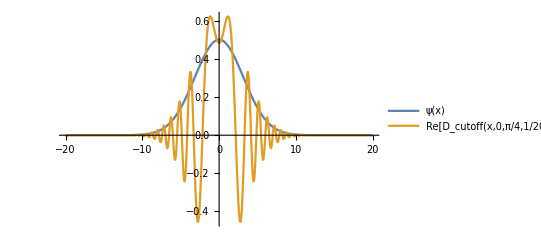

psiandkern.eps

```mathematica
modeno=20;
atomwidth=Sqrt[modeno/4]
plot3=Plot[{Psi[x,atomwidth],Re[KernCutoff[x,0,Pi/4,1/modeno]]},{x,-20,20},PlotRange->All,PlotLegends->Placed[{"ψ(x)","Re[D_cutoff(x,0,π/4,1/20)]"},Above]]
Export["psiandkern.eps",plot3]
```

```mathematica
X[x_,xp_,θ_,σ_]=Integrate[Kern1D[x,xpp,θ]*Abs[Psi[xpp,σ]]^2*Kern1D[xpp,xp,-θ],{xpp,-∞,∞},Assumptions->σ ∈Reals&&σ>0];
```

```mathematica
modes=20;
σP=Sqrt[modes/4];
γP=1/modes;
```

```mathematica
XCO[x_,xp_,ξ_,γ_]=Integrate[KernCutoff[x,xpp,ξ,γ]*Abs[Psi[xpp,σP]]^2*KernCutoff[xpp,xp,-ξ,γ],{xpp,-∞,∞}];
```

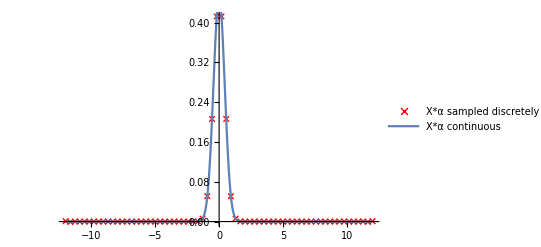

```mathematica
points=64;
ls=12;
L=ls*2/(points+1);
XCOdisc[x_,xp_]=Sum[L*KernCutoff[x,xpp,Pi/4,γP]*Abs[Psi[xpp,σP]]^2*KernCutoff[xpp,xp,-Pi/4,γP],{xpp,-ls,ls,L}];
XCOdisctable=Table[{x,Re[XCOdisc[x,0]]},{x,-ls,ls,L}];
Show[{ListPlot[XCOdisctable,PlotRange->Full,PlotMarkers->{Style["×",Red],Medium},PlotLegends->Placed[{"X*α sampled discretely"},Above]],Plot[Re[XCO[x,0,Pi/4,γP]],{x,-ls,ls},PlotRange->Full,PlotLegends->Placed[{"X*α continuous"},Above]]}]
```

```mathematica
(* Continuous version of what the integral of X.α would be *)
```

```mathematica
XαCO[x_]=Integrate[XCO[x,xp]*alpha[xp],{xp,-∞,∞}];
```

```mathematica
XαCOdisc[x_]=Sum[L*XCOdisc[x,xp]*alpha[xp],{xp,-ls,ls,L}];
XαCOdisctable=Table[{x,Re[XαCOdisc[x]]},{x,-ls,ls,L}];
```

Table::iterb: Iterator {x,-ls,ls,L} does not have appropriate bounds.

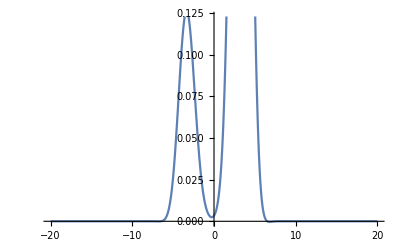

```mathematica
Plot[Re[XαCO[x]],{x,-20,20}]
```

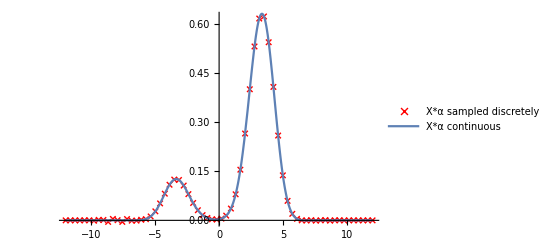

```mathematica
plot1=Show[{ListPlot[XαCOdisctable,PlotRange->All,PlotMarkers->{Style["×",Red],Medium},PlotLegends->Placed[{"X*α sampled discretely"},Above]],Plot[Re[XαCO[x]],{x,-ls,ls},PlotRange->All,PlotLegends->Placed[{"X*α continuous"},Above]]}]
```

```mathematica
Export["Xalpha"<> ToString[modes]<>"modes"<>ToString[points]<>"grid.eps",plot1]
```

Xalpha20modes64grid.eps

## α(r) with mode cutoff, smoothing, even modes only

```mathematica
(* The int term contains a double convolution with the atom field intensity, which is smooth -- assume Gaussian. We also take alpha to be some smooth function to compare things *)
Clear[σ]
shiftpsi=0;
shiftalpha=-4;
peakalpha=5;
(*σP=20;*)
Psi[x_,σ_]=1/Sqrt[Sqrt[Pi] σ](Exp[-(x-shiftpsi)^2/(4 σ^2)]);
alpha[xp_]=Exp[-(xp-shiftalpha)^2/2]+peakalpha*Exp[-(xp+shiftalpha)^2/2];
plot2=Plot[{Psi[x,Sqrt[20]],alpha[x]},{x,-20,20},PlotLegends->{"Psi","alpha"}, PlotRange->All]
(*Export["wavefns.png",plot2]*)
```

-Graphics-

```mathematica
(* to only keep even m+n modes, we need to make the kernel with the correct parity *)
KernCutoff[x_,xp_,ξ_,γ_]=Sqrt[ⅈ/(2*Pi*Sin[ξ+ⅈ γ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
KernEven[x_,xp_,y_,yp_,ξ_,γ_]=0.5*(KernCutoff[x,xp,ξ,γ]*KernCutoff[y,yp,ξ,γ]+KernCutoff[x,-xp,ξ,γ]*KernCutoff[y,-yp,ξ,γ]);
```

```mathematica
(* We want to try convolving the kernels with a smoothing function on the scale of the lattice spacing -- here take a Gaussian smoothing fn 01 *)
SmoothingFn[x_,y_,xp_,yp_,L_]=1/(2 Pi L^2)*Exp[-(x-y)^2/(2L^2)-(xp-yp)^2/(2L^2)];
```

```mathematica
(* We want to get a function S=int dx int dxp D(r,r',ξ) Smoothing(r,r') -- coefficients for a single kernel contr K(x,xp,ξ)*Smoothing(x,xp) gotten by pen and paper *)
```

```mathematica
Clear[L]
α[ξ_,L_]=ⅈ/(2 Tan[ξ])+1/(2L^2);
β[ξ_,L_]=α[ξ,L]+1/(4*α[ξ,L]*Sin[ξ]^2);
A[ξ_,L_]=1/(2Pi L^2)*Sqrt[(ⅈ*Pi)/(β[ξ,L]*α[ξ,L]*Sin[ξ])];
B[ξ_,L_]=1/(2L^2)-1/(4L^4*β[ξ,L]);
Cc[ξ_,L_]=ⅈ/(4*L^4*α[ξ,L]*β[ξ,L]*Sin[ξ]);
S[x_,xp_,ξ_,L_]=A[ξ,L]*Exp[-B[ξ,L]*(x^2+xp^2)-Cc[ξ,L]*x*xp];
```

```mathematica
(* Then for the right parity kernel: *)
SEven[x_,xp_,y_,yp_,ξ_,γ_,L_]=0.5*(S[x,xp,ξ+ⅈ γ,L]*S[y,yp,ξ+ⅈ γ,L]+S[x,-xp,ξ+ⅈ γ,L]*S[y,-yp,ξ+ⅈ γ,L]);
```

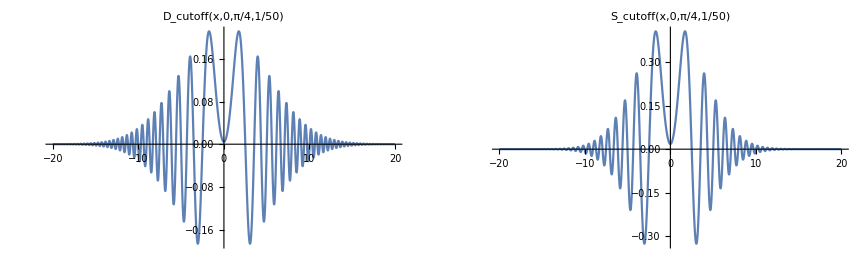

```mathematica
GraphicsGrid[{{Plot[Re[KernEven[x,0,0,0,Pi/4,1/50]],{x,-20,20},ImageSize->400,PlotLabel->"D_cutoff(x,0,π/4,1/50)"],
Plot[Re[SEven[x,0,0,0,Pi/4,1/50,0.1]],{x,-20,20},ImageSize->400,PlotLabel->"S_cutoff(x,0,π/4,1/50)",PlotRange->All]}}]
```

```mathematica
modes=20;
σP=Sqrt[modes/4];
γP=1/modes;
```

```mathematica
Timing[ XEven[x_,xp_,ξ_,γ_]=Integrate[KernEven[x,xpp,0,0,ξ,γ]*Abs[Psi[xpp,σP]]^2*KernEven[xpp,xp,0,0,-ξ,γ],{xpp,-∞,∞}];]
```

{432.964,Null}

```mathematica
Timing[XEvenSmooth[x_,xp_,ξ_,γ_,l_]=Integrate[SEven[x,xpp,0,0,ξ,γ,l]*Abs[Psi[xpp,σP]]^2*SEven[xpp,xp,0,0,-ξ,γ,l],{xpp,-∞,∞},Assumptions->l∈Reals&&l>0];]
```

{580.808,Null}

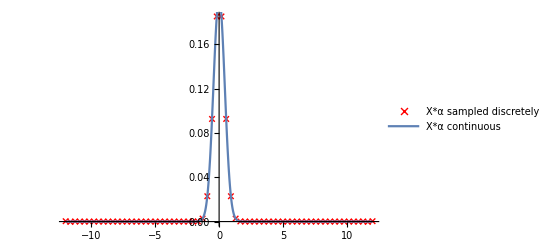

```mathematica
points=64;
ls=12;
L=ls*2/(points+1);
XEvendisc[x_,xp_]=Sum[L*KernEven[x,xpp,0,0,Pi/4,γP]*Abs[Psi[xpp,σP]]^2*KernEven[xpp,xp,0,0,-Pi/4,γP],{xpp,-ls,ls,L}];
XEvendisctable=Table[{x,Re[XEvendisc[x,0]]},{x,-ls,ls,L}];
Show[{ListPlot[XEvendisctable,PlotRange->Full,PlotMarkers->{Style["×",Red],Medium},PlotLegends->Placed[{"X*α sampled discretely"},Above]],Plot[Re[XEven[x,0,Pi/4,γP]],{x,-ls,ls},PlotRange->Full,PlotLegends->Placed[{"X*α continuous"},Above]]}]
```

```mathematica
Print[N[L]]
```

0.369231

0.2

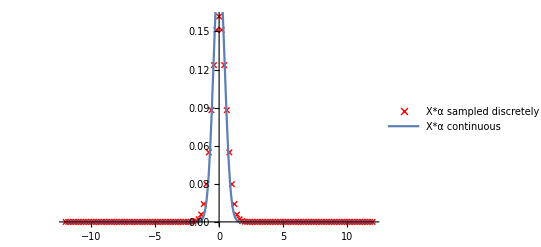

```mathematica
sm=0.2
XEvenSmoothdisc[x_,xp_]=Sum[L*SEven[x,xpp,0,0,Pi/4,γP,L/2]*Abs[Psi[xpp,σP]]^2*SEven[xpp,xp,0,0,-Pi/4,γP,L/2],{xpp,-ls,ls,L}];
XEvenSmoothdisctable=Table[{x,Re[XEvenSmoothdisc[x,0]]},{x,-ls,ls,sm}];
Show[{ListPlot[XEvenSmoothdisctable,PlotRange->Full,PlotMarkers->{Style["×",Red],Medium},PlotLegends->Placed[{"X*α sampled discretely"},Above]],Plot[Re[XEven[x,0,Pi/4,γP]],{x,-ls,ls},PlotRange->Full,PlotLegends->Placed[{"X*α continuous"},Above]]}]
```

## Integrating light field EoM analytically in k-space to figure out what is happening to data

```mathematica
int1=Integrate[ Exp[-a x^2+b x],{x,-∞,∞},Assumptions->Re[a]>0&&Re[c]>0&&Re[-4 c+e^2/a]<0];
int2=Integrate[ AA*Exp[-a x^2+b x],{x,-∞,∞},Assumptions->Re[a]>0&&Re[c]>0&&Re[-4 c+e^2/a]<0];
```

```mathematica
E0=1;
L=0.5;
ξ=Pi/4;
σ=1;
```

```mathematica
Clear[E0,L,ξ,σ,σL]
```

```mathematica
~
```

```mathematica
replacements[x_,xpp_]={a->(1/(2σA^2)),b->-ⅈ/Sin[ξ+ⅈ γ]*(x+xpp)}
```

{a→1/(2 σA^2),b→-(x+xpp) Csch[γ-ⅈ ξ]}

```mathematica
res[x_,xpp_]=FullSimplify[int1/.replacements[x,xpp],Assumptions->ξ∈Reals]
```

(ⅇ^(1/2 (x+xpp)^2 σA^2 Csch[γ-ⅈ ξ]^2) √(2 π))/(√(1/σA^2))

At this point, the integrals look like the following, where we want to do x’’ and y’’ next:

=...-E_0/4 1/(16 π^2 sin^2 θ_0)∫ⅆk'α(k’)∫ⅆr e^-ikr exp[-ⅈ/(2 tan θ_0) *(|r|)^2] exp[-σ^2/(2 sin^2 θ_0)(|r|)^2] ∫ⅆx’’ ∫ⅆy’’ exp[-σ^2/(2 sin^2 θ_0)( x''^2+2x x'')]exp[-σ^2/(2 sin^2 θ_0)(y''^2+2 y y'')] exp[ⅈ/(2 tan θ_0) (x''^2+y''^2)] e^(ik_x x''+ik_y y'')

```mathematica
replacements2[x_,kp_]={a->(σ^2/(2 Sin[ξ+ⅈ γ]^2)-ⅈ/(2 Tan[ξ+ⅈ γ])),b->ⅈ kp-σ^2/Sin[ξ+ⅈ γ]^2 x}
```

{a→-1/2 Coth[γ-ⅈ ξ]-1/2 σ^2 Csch[γ-ⅈ ξ]^2,b→ⅈ kp+x σ^2 Csch[γ-ⅈ ξ]^2}

```mathematica
res2[x_,kp_]=FullSimplify[int1/.replacements2[x,kp],Assumptions->ξ∈Reals&&σ∈Reals]
```

(2 ⅇ^(((kp-ⅈ x σ^2 Csch[γ-ⅈ ξ]^2)^2)/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2))) √π)/(√(-Csch[γ-ⅈ ξ]^2 (2 σ^2+Sinh[2 γ-2 ⅈ ξ])))

```mathematica
exponents2=CoefficientList[((kp-ⅈ x σ^2 Csch[γ-ⅈ ξ]^2)^2)/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2)),x]
```

{kp^2/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2)),-(ⅈ kp σ^2 Csch[γ-ⅈ ξ]^2)/(Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2),-(σ^4 Csch[γ-ⅈ ξ]^4)/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2))}

```mathematica
replacements3[k_,kp_]={AA->Exp[exponents2[[1]]],a->ⅈ/(2 Tan[ξ+ⅈ γ])+σ^2/(2 Sin[ξ+ⅈ γ]^2)-exponents2[[3]],b->exponents2[[2]]-ⅈ k}
```

{AA→ⅇ^(kp^2/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2))),a→1/2 Coth[γ-ⅈ ξ]-1/2 σ^2 Csch[γ-ⅈ ξ]^2+(σ^4 Csch[γ-ⅈ ξ]^4)/(2 (Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2)),b→-ⅈ k-(ⅈ kp σ^2 Csch[γ-ⅈ ξ]^2)/(Coth[γ-ⅈ ξ]+σ^2 Csch[γ-ⅈ ξ]^2)}

```mathematica
res3[k_,kp_]=FullSimplify[int2/.replacements3[k,kp] ,Assumptions->ξ∈Reals&&σ∈Reals]
```

(ⅇ^(-1/4 (k+kp) Sech[γ-ⅈ ξ]^2 (2 (k+kp) σ^2+(k-kp) Sinh[2 γ-2 ⅈ ξ])))/(√(Cosh[γ-ⅈ ξ]^2/(2 π σ^2+π Sinh[2 γ-2 ⅈ ξ])))

```mathematica
(*LaunchKernels[2]*)
```

```mathematica
(*CloseKernels[]*)
```

```mathematica
(*intTerm[kp_]=Timing[Parallelize[Sum[res3[k,kp],{k,500}]];]*)
```

```mathematica
alpha[kp_]=σL/Sqrt[2 Pi] Exp[-σL^2/2 kp^2]
```

(ⅇ^(-1/2 kp^2 σL^2) σL)/(√(2 π))

```mathematica
ξ=Pi/4;
σ=3;
σL=5;
γ=1/20;
```

```mathematica
interaction[k_,ξ_,σ_,σL_,γ_]=Integrate[res3[k,kp]*alpha[kp],{kp,-∞,∞},Assumptions->ξ>0&&σ>0&&σL>0]
```

(5 ⅇ^(((13+451 ⅈ ⅇ^(1/10)+12 ⅇ^(1/5)) k^2)/(26-86 ⅈ ⅇ^(1/10)-24 ⅇ^(1/5))))/(√((-13+43 ⅈ ⅇ^(1/10)+12 ⅇ^(1/5))/((1+36 ⅈ ⅇ^(1/10)+ⅇ^(1/5)) π)))

```mathematica
Manipulate[Plot[Abs[interaction[k,ξ,σ,σL,1/modeno]],{k,-10,10}],{{ξ,Pi/4},0.001,Pi/2},{σ,0.5,10,0.5},{σL,0.5,10,0.5},{{modeno,20},10,50,1}]
```

```mathematica
Clear[E0,L,ξ,σ,σL]
```

```mathematica
Integrate[1/Pi*Exp[ⅈ z Cos[θ]],{θ,0, Pi}]
```

ConditionalExpression[BesselJ[0,Abs[z]],z∈Reals]

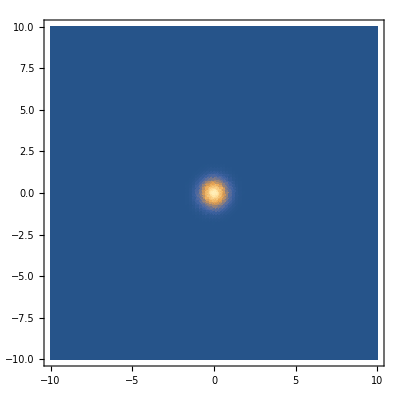

```mathematica
aa=2; bb=2;cc=0.2;
DensityPlot[Abs[Exp[-(aa +ⅈ bb)(x^2+y^2)]],{x,-10,10},{y,-10,10},PlotPoints->100,PlotRange->All]
```

## α(r) with mode cutoff,even modes only, Gaussian light field and atomic field to compare numerics

```mathematica
psi[x_,y_,σA_]=1/Sqrt[Sqrt[Pi] σA](Exp[-(x^2+y^2)/(4 σA^2)]);
alpha[x_,y_,σL_]=1/Sqrt[Sqrt[Pi] σL](Exp[-(x^2+y^2)/(4 σL^2)]);
```

```mathematica
(* to only keep even m+n modes, we need to make the kernel with the correct parity *)
KernCutoff[x_,xp_,ξ_,γ_]=Sqrt[ⅈ/(Pi*Sin[ξ+ⅈ γ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
KernEven[x_,xp_,y_,yp_,ξ_,γ_]=0.5*(KernCutoff[x,xp,ξ,γ]*KernCutoff[y,yp,ξ,γ]+KernCutoff[x,-xp,ξ,γ]*KernCutoff[y,-yp,ξ,γ])
```

0.5 ((ⅇ^(-1/2 ⅈ (-ⅈ (x^2+xp^2) Coth[γ-ⅈ ξ]-2 ⅈ x xp Csch[γ-ⅈ ξ])-1/2 ⅈ (-ⅈ (y^2+yp^2) Coth[γ-ⅈ ξ]-2 ⅈ y yp Csch[γ-ⅈ ξ])) Csch[γ-ⅈ ξ])/π+(ⅇ^(-1/2 ⅈ (-ⅈ (x^2+xp^2) Coth[γ-ⅈ ξ]+2 ⅈ x xp Csch[γ-ⅈ ξ])-1/2 ⅈ (-ⅈ (y^2+yp^2) Coth[γ-ⅈ ξ]+2 ⅈ y yp Csch[γ-ⅈ ξ])) Csch[γ-ⅈ ξ])/π)

```mathematica
KernEvenNine[x_,xp_,y_,yp_,ξ_,γ_]=ⅈ/(2 π Sin[ξ + ⅈ γ])*(Exp[(-ⅈ/2)*((x*x+xp*xp+y*y+yp*yp)/Tan[ξ+ⅈ*γ]-(2*x*xp+2*y*yp)/Sin[ξ+ⅈ γ])]+Exp[(-ⅈ/2)*((x*x+xp*xp+y*y+yp*yp)/Tan[ξ+ⅈ*γ]+(2*x*xp+2*y*yp)/Sin[ξ+ⅈ γ])])
```

1/(2 π)(ⅇ^(-1/2 ⅈ (-ⅈ (x^2+xp^2+y^2+yp^2) Coth[γ-ⅈ ξ]-ⅈ (2 x xp+2 y yp) Csch[γ-ⅈ ξ]))+ⅇ^(-1/2 ⅈ (-ⅈ (x^2+xp^2+y^2+yp^2) Coth[γ-ⅈ ξ]+ⅈ (2 x xp+2 y yp) Csch[γ-ⅈ ξ]))) Csch[γ-ⅈ ξ]

```mathematica
Simplify[KernEven[x,xp,y,yp,Pi/4,1/20]==KernEvenNine[x,xp,y,yp,Pi/4,1/20]]
```

True

```mathematica
modes=20;
σL=2;
σA=Sqrt[modes/4];
```

```mathematica
X[x_,xp_]=Integrate[KernEven[x,xpp,0,0,Pi/4,1/modes]*Abs[psi[xpp,0,σA]]^2*KernEven[xpp,xp,0,0,-Pi/4,1/modes],{xpp,-∞,∞}]
```

ⅇ^(1/2 (-x^2 Coth[1/20 (1-5 ⅈ π)]-xp^2 Coth[1/20 (1+5 ⅈ π)])) ((0.1009-8.60124×10^-19 ⅈ) ⅇ^((5 (1+ⅇ^(1/5)) (x Csch[1/20 (1-5 ⅈ π)]-xp Csch[1/20 (1+5 ⅈ π)])^2)/(-18+22 ⅇ^(1/5)))+(0.1009-8.60124×10^-19 ⅈ) ⅇ^((5 (1+ⅇ^(1/5)) (x Csch[1/20 (1-5 ⅈ π)]+xp Csch[1/20 (1+5 ⅈ π)])^2)/(-18+22 ⅇ^(1/5))))

```mathematica
IntLight[x_]=Integrate[X[x,xp]*alpha[xp,0,σL],{xp,-∞,∞}]
```

(0.117601+0.00564034 ⅈ) ⅇ^(-((-63+2 ⅈ ⅇ^(1/10)+99 ⅇ^(1/5)) x^2)/(2 (63-16 ⅈ ⅇ^(1/10)+99 ⅇ^(1/5))))

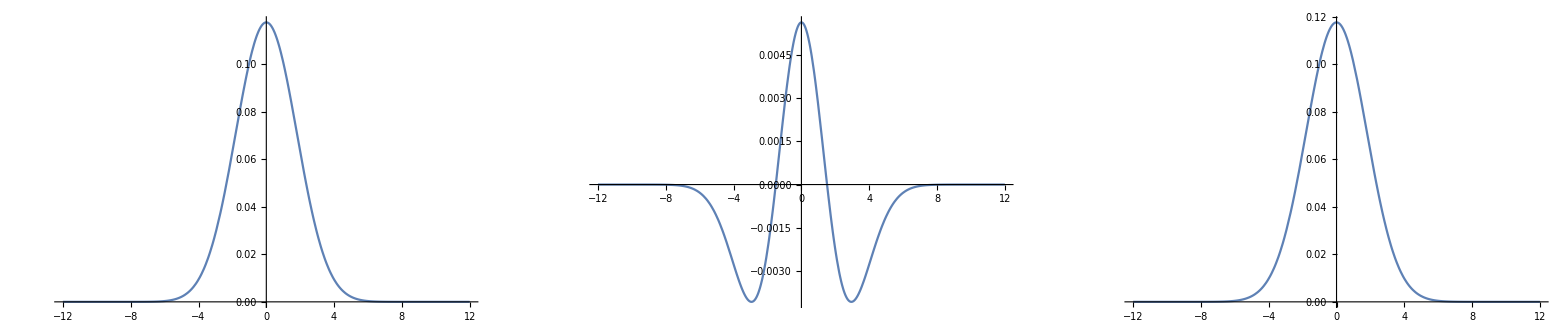

```mathematica
GraphicsGrid[{{Plot[Re[IntLight[x]],{x,-12,12},ImageSize->500],Plot[Im[IntLight[x]],{x,-12,12}],Plot[Abs[IntLight[x]],{x,-12,12}]}}]
```

## Rotationally symmetric stuff

```mathematica
(*2D:*)
```

```mathematica
Psi[x_,y_]=1/(Sqrt[2 π] σA)*Exp[-(x^2+y^2)/(4 σA^2)];
```

```mathematica
σA=Sqrt[5];
```

```mathematica
Integrate[Psi[x,y]^2,{x,-∞,∞},{y,-∞,∞}]
```

1

```mathematica
(*In only r*)
```

```mathematica
Psi1D[r_]=1/(Sqrt[2 π] σA)*Exp[-r^2/(4 σA^2)];
```

```mathematica
(*This is still normalised:*)
```

```mathematica
Integrate[r Psi1D[r]^2,{r,0,∞},{θ,0,2Pi},Assumptions->σA>0]
```

1

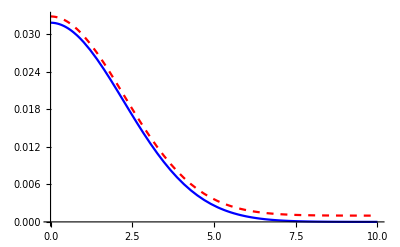

```mathematica
Plot[{Psi[x,0]^2,Psi1D[x]^2+0.001},{x,0,10},PlotStyle->{Blue,{Red,Dashed}}]
```

```mathematica
(*N[Psi[0,0]]
N[Psi1D[0]]
GraphicsGrid[{{Plot3D[Psi[x,y],{x,-12,12},{y,-12,12},PlotRange->All],
RevolutionPlot3D[Psi1D[r],{r,0,12},{θ,0,2 Pi}]}}]
*)
```

```mathematica
Pump[x_,y_,f0_,D0_]=-f0/(D0+ⅈ κ)*Exp[-(x^2+y^2)/(2 σ^2)];
κ=0.8;σ=2;
```

```mathematica
KernCutoff[x_,xp_,ξ_,γ_]=Sqrt[ⅈ/(2*Pi*Sin[ξ+ⅈ γ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
```

```mathematica
KernEven[x_,xp_,y_,yp_,ξ_,γ_]=0.5*(KernCutoff[x,xp,ξ,γ]*KernCutoff[y,yp,ξ,γ]+KernCutoff[x,-xp,ξ,γ]*KernCutoff[y,-yp,ξ,γ]);
```

```mathematica
Integrate[Exp[-ⅈ A Cos[θ-θp]]+Exp[ⅈ A Cos[θ-θp]],{θp,0,2Pi}, Assumptions->A>0]
```

4 π BesselJ[0,A]

```mathematica
(*A here is  (r rp)/Sin[ξ+ⅈ ξ] so prefactor for rotationally symmetric kernel is *)
```

```mathematica
FullSimplify[ⅈ/(2*Pi*Sin[ξ+ⅈ γ])*1/2*4Pi]
```

Csch[γ-ⅈ ξ]

```mathematica
KernRot[r_,rp_,ξ_,γ_]=ⅈ/Sin[ξ+ⅈ γ]*Exp[-ⅈ/2((r^2+rp^2)/Tan[ξ+ⅈ γ])]BesselJ[0,(r *rp)/Sin[ξ+ⅈ γ]];
```

```mathematica
(* CAN DO EXACT -- NO NEED FOR γ *)
```

```mathematica
Int2D[x_,y_,ξ_,f0_,D0_]=Integrate[KernEven[x,xp,y,yp,ξ,0]*Pump[xp,yp,f0,D0],{xp,-∞,∞},{yp,-∞,∞},Assumptions->x∈Reals&&y∈Reals&&ξ>0&&f0>0&&D0>0]
```

```mathematica
Int2D[x_,y_,ξ_,f0_,D0_]=-((0.+3.999999999999999 ⅈ) ⅇ^(((x^2+y^2) (-4 ⅈ+Cot[ξ]))/(2 ⅈ-8 Cot[ξ])) f0 Csc[ξ])/(((0.+0.8 ⅈ)+D0) (1+4 ⅈ Cot[ξ]));
```

```mathematica
(*Int1D[r_,ξ_,f0_,D0_]=Integrate[rp KernRot[r,rp,ξ,0]*Pump[rp,0,f0,D0],{rp,0,∞},Assumptions->r>0&&σ>0&&f0>0&&D0>0&&ξ>0]*)
```

```mathematica
Int1D[r_,ξ_,f0_,D0_]=-(4 ⅇ^((r^2 (-4 ⅈ+Cot[ξ]))/(2 ⅈ-8 Cot[ξ])) f0 Csc[ξ])/(((0.+0.8 ⅈ)+D0) (-ⅈ+4 Cot[ξ]));
```

```mathematica
(*GraphicsGrid[{{Plot[Re[KernEven[r,1,0,0,Pi/4,1/20]],{r,0,12},ImageSize->300],Plot[Im[KernEven[r,1,0,0,Pi/4,1/20]],{r,0,12},PlotStyle->Orange]}}]
GraphicsGrid[{{Plot[Re[KernRot[r,1,Pi/4,1/20]],{r,0,12},ImageSize->300],Plot[Im[KernRot[r,1,Pi/4,1/20]],{r,0,12},PlotStyle->Orange,PlotRange->All]}}]*)
```

```mathematica
(*Plot3D[Abs[Int2D[x,y]],{x,-12,12},{y,-12,12},PlotRange->All,PlotRange->All,ImageSize->500,PlotPoints->50]
RevolutionPlot3D[Abs[Int1D[r]],{r,0,12},{θ,0,2 Pi},PlotRange->All,ImageSize->500]*)
```

```mathematica
(*Manipulate[Plot[{Re[Pump[x,0,10,D]],Im[Pump[x,0,10,D]],Abs[Pump[x,0,10,D]]},{x,0,12},PlotRange->All,PlotStyle->{Blue,Red,Yellow},PlotLegends->{"Re","Im","Abs"}],{D,-10,10,2}]*)
```

```mathematica
(*Y=0;
f0curr=10;
D0curr=10;
GraphicsGrid[{{Plot[Re[Int2D[r,Y,Pi/4,f0curr,D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int2D[r,Y,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int2D[r,Y,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D cut of 2D Kernel convolved with 2D pump term"]
GraphicsGrid[{{Plot[Re[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D Kernel convolved with 1D pump term"]
*)
```

```mathematica
(*Y=0;
f0curr=10;
D0curr=10;
GraphicsGrid[{{Plot[Re[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"D(r,r')*f(r,D0)"]
GraphicsGrid[{{Plot[Re[Int1D[r,Pi/4,f0curr,-D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int1D[r,Pi/4,f0curr,-D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int1D[r,Pi/4,f0curr,-D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"D(r,r')*f(r,-D0)"]
*)
```

```mathematica
(*Y=0;
f0curr=10;
D0curr=10;
GraphicsGrid[{{Plot[Re[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int1D[r,Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"D(r,r',Pi/4)*f(r,D0)"]
GraphicsGrid[{{Plot[Re[Int1D[r,-Pi/4,f0curr,D0curr]],{r,0,12},ImageSize->300,PlotRange->All],Plot[Im[Int1D[r,-Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Int1D[r,-Pi/4,f0curr,D0curr]],{r,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"D(r,r',-Pi/4)*f(r,D0)"]
*)
```

```mathematica
ωT=0.1;η=1;E0=10;
```

```mathematica
pot1[r_]=(ωT r^2)/(2 η);
```

1

10

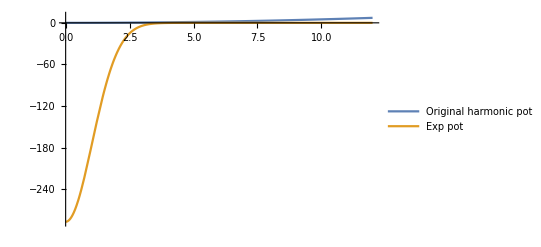

```mathematica
D0temp=1
fPtemp=10
pot2[r_]=-(E0/4)Abs[Int1D[r,Pi/4,fPtemp,D0temp]]^2;
min=pot2[0];
max=pot1[12];
Plot[{pot1[r],pot2[r]},{r,0,12},PlotRange->{{0,12},{min-0.2,max+2}},PlotLegends->{"Original harmonic pot","Exp pot"}]
```

```mathematica
(*Afit=0.005*)
```

```mathematica
(*lsho=N[(1/30)/(2*Afit)]*)
```

## Getting some sense of how D(x,x’,ξ) and D(x,x’,-ξ) compare

```mathematica
KernCutoff[x_,xp_,ξ_,γ_]=Sqrt[ⅈ/(2*Pi*Sin[ξ+ⅈ γ])]*Exp[-ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
```

```mathematica
KernEven[x_,xp_,y_,yp_,ξ_,γ_]=0.5*(KernCutoff[x,xp,ξ,γ]*KernCutoff[y,yp,ξ,γ]+KernCutoff[x,-xp,ξ,γ]*KernCutoff[y,-yp,ξ,γ]);
```

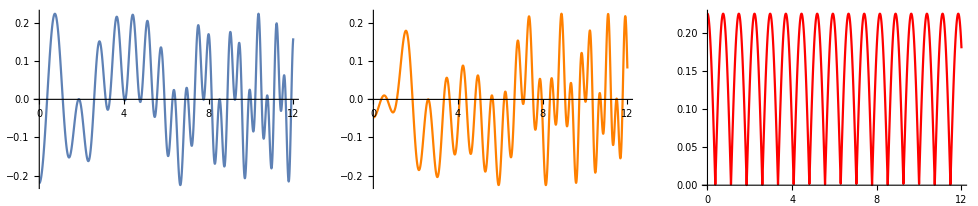

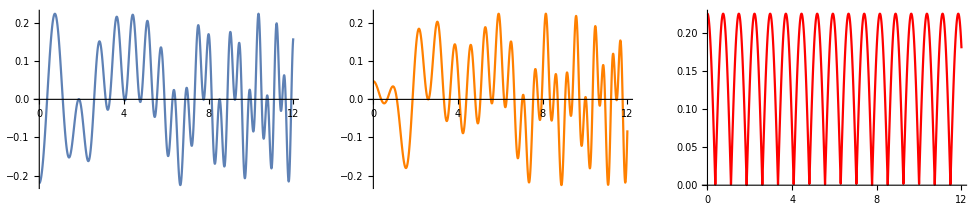

```mathematica
XP=3;
YY=0;
YP=0;
ξP=π/4;
γP=0;
GraphicsGrid[{{Plot[Re[KernEven[x,XP,YY,YP,ξP,γP]],{x,0,12},ImageSize->300,PlotRange->All],Plot[Im[KernEven[x,XP,YY,YP,ξP,γP]],{x,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[KernEven[x,XP,YY,YP,ξP,γP]],{x,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D cut of Kernel"]
GraphicsGrid[{{Plot[Re[KernEven[x,XP,YY,YP,-ξP,γP]],{x,0,12},ImageSize->300,PlotRange->All],Plot[Im[KernEven[x,XP,YY,YP,-ξP,γP]],{x,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[KernEven[x,XP,YY,YP,-ξP,γP]],{x,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D Kernel convolved with 1D pump term"]
```

```mathematica
Im[KernCutoff[1,1,a,0]]==Im[KernCutoff[1,1,-a,0]]
```

Im[ⅇ^(-1/2 ⅈ (2 Cot[a]-2 Csc[a])) √(ⅈ Csc[a])]/(√(2 π))==Im[ⅇ^(-1/2 ⅈ (-2 Cot[a]+2 Csc[a])) √(-ⅈ Csc[a])]/(√(2 π))

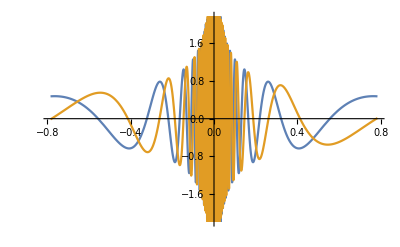

```mathematica
Plot[{Re[KernCutoff[3,1,a,0]],Im[KernCutoff[3,1,a,0]]},{a,-π/4,π/4}]
```

## Fixed factors in D(x,x’,ξ), comparing magnitudes

```mathematica
Kern[x_,xp_,ξ_,γ_]=Sqrt[1/(ⅈ*Pi*Sin[ξ+ⅈ γ])]*Exp[ⅈ/2((xp^2+x^2)/Tan[ξ+ⅈ γ]-(2*xp*x)/Sin[ξ+ⅈ γ])];
```

```mathematica
Dkern[x_,xp_,y_,yp_,ξ_,γ_]=0.5*(Kern[x,xp,ξ,γ]*Kern[y,yp,ξ,γ]+Kern[x,-xp,ξ,γ]*Kern[y,-yp,ξ,γ]);
```

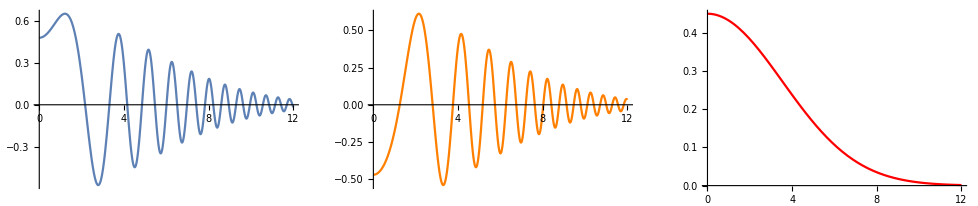

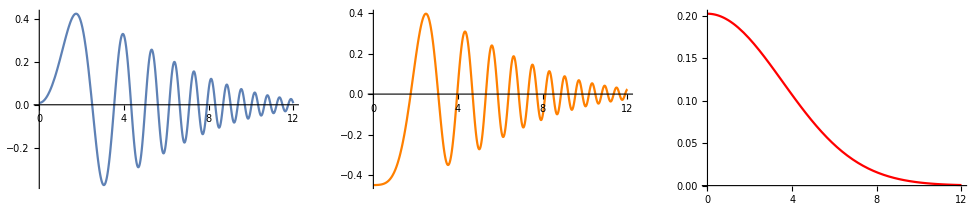

```mathematica
XP=0;
YY=0;
YP=0;
ξP=Pi/4;
γP=-1/50;
GraphicsGrid[{{Plot[Re[Kern[x,XP,ξP,γP]],{x,0,12},ImageSize->300,PlotRange->All],Plot[Im[Kern[x,XP,ξP,γP]],{x,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Kern[x,XP,ξP,γP]]^2,{x,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D cut of Kernel"]
GraphicsGrid[{{Plot[Re[Dkern[x,XP,YY,YP,ξP,γP]],{x,0,12},ImageSize->300,PlotRange->All],Plot[Im[Dkern[x,XP,YY,YP,ξP,γP]],{x,0,12},PlotStyle->Orange,PlotRange->All],Plot[Abs[Dkern[x,XP,YY,YP,ξP,γP]]^2,{x,0,12},PlotStyle->Red,PlotRange->All]}},PlotLabel->"1D cut of Kernel"]
```

```mathematica
Psi[x_,y_,σ_]=1/(Sqrt[2 π] σ)*Exp[-(x^2+y^2)/(4 σ^2)];
Alpha[x_,y_,σ_,fP_,D0_,kappa_]=-1/(D0-ⅈ kappa)fP*Exp[-(x^2+y^2)/(4 σ^2)];
```

```mathematica
Alpha[x_,y_,σ_,fP_]=fP*Exp[-(x^2+y^2)/(2 σ^2)];
```

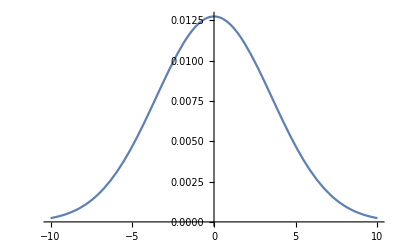

```mathematica
Plot[Abs[Psi[x,0,3.53553390593273]]^2,{x,-10,10}]
```

```mathematica
X[x_,xpp_,σ_]=Integrate[Dkern[x,xp,0,0,Pi/4,0]*Dkern[xp,xpp,0,0,Pi/4,0]*Abs[Psi[xp,0,σ]]^2,{xp,-∞, ∞},Assumptions->σ∈Integers&&σ>0]
```

(ⅇ^(-((x^2+xpp^2) (1+2 ⅈ σ^2))/(2 ⅈ+4 σ^2)) (-0.0404213 ⅇ^((ⅈ (x-xpp)^2 σ^2)/(ⅈ+2 σ^2))-0.0404213 ⅇ^((ⅈ (x+xpp)^2 σ^2)/(ⅈ+2 σ^2))))/(σ √(1-2 ⅈ σ^2))

```mathematica
lightint[x_]=Integrate[X[x,xpp,3]*Alpha[xpp,0,2,11],{xpp,-∞,∞}]
```

(-0.296875-0.285676 ⅈ) ⅇ^((-1881/677+(353 ⅈ)/1354) x^2)

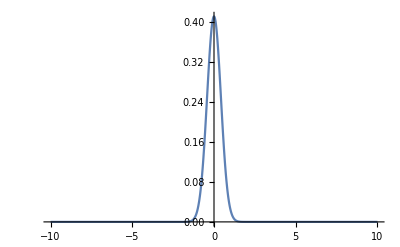

```mathematica
Plot[Abs[lightint[x]],{x,-10,10},PlotRange->All]
```

```mathematica
(* Trying to check the magnitude that mod sq alpha should output first few steps *)
```

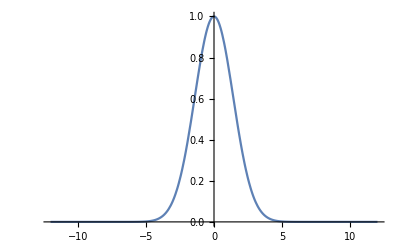

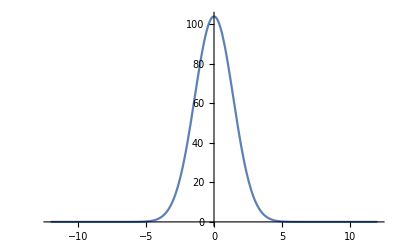

```mathematica
alp[x_,fP_,σ_,Delta0_,kappa_]=Abs[-ⅈ((Delta0-ⅈ kappa)Alpha[x,0,σ,fP]+Alpha[x,0,σ,fP])]^2;
Plot[Alpha[x,0,2,1]^2,{x,-12,12}]
Plot[alp[x,1,2,1,10],{x,-12,12}]
```

## Integratin stuff

```mathematica
phiarg[x_,xp_]=Exp[-xp^2/(2 σ^2)]*1/Sqrt[ⅈ π Sin[ξ]]*Exp[ⅈ/2((x^2+xp^2)/Tan[ξ]-(2 x xp)/Sin[ξ])];
```

```mathematica
int=Integrate[ AA*Exp[-a x^2+b x],{x,-∞,∞},Assumptions->Re[a]>0&&Re[c]>0&&Re[-4 c+e^2/a]<0];
```

```mathematica
replacements[x_]={AA->1/Sqrt[ⅈ π Sin[ξ]]*Exp[ⅈ/2 x^2/Tan[ξ]] ,a->(1/(2σ^2)-ⅈ/(2Tan[ξ])),b->-ⅈ/Sin[ξ]x}
```

{AA→(ⅇ^(1/2 ⅈ x^2 Cot[ξ]))/(√π √(ⅈ Sin[ξ])),a→1/(2 σ^2)-1/2 ⅈ Cot[ξ],b→-ⅈ x Csc[ξ]}

```mathematica
res[x_,xpp_]=FullSimplify[int/.replacements[x],Assumptions->ξ∈Reals]
```

(√2 ⅇ^((x^2 (-ⅈ σ^2-Cot[ξ]))/(2 ⅈ+2 σ^2 Cot[ξ])))/(√(1/σ^2-ⅈ Cot[ξ]) √(ⅈ Sin[ξ]))

```mathematica
FullSimplify[(-ⅈ σ^2-Cot[ξ])/(2 ⅈ+2 σ^2 Cot[ξ])]
```

-(ⅈ σ^2+Cot[ξ])/(2 ⅈ+2 σ^2 Cot[ξ])

```mathematica
FullSimplify[Tanh[ⅈ x]]
```

ⅈ Tan[x]

## (ⅇ^(-r^2/(2 σ^2)) fP)/(Δ-ⅈ κ)

(ⅇ^(-r^2/(2 σ^2)) fP)/(Δ-ⅈ κ)

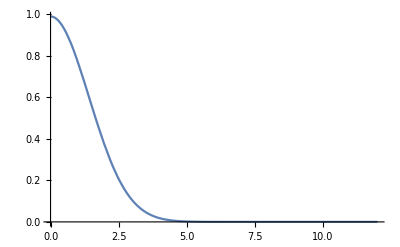

```mathematica
fun[r_,fP_,σ_,Δ_,κ_]=fP Exp[-r^2/(2 σ^2)]*1/(Δ-ⅈ κ)
Plot[Abs[fun[r,1000,2,100,1000]]^2,{r,0,12}]
```